```mathematica
connectOneBarabasiAlbert[g_Graph/;ConnectedGraphQ[g]]:=g;
connectOneBarabasiAlbert[g_Graph]:=Module[{cmps=ConnectedComponents[g],pos},
pos=Flatten[Intersection[Position[VertexInDegree[seed],0],Select[cmps,Length[#]==Min[Length/@cmps]&]]];
If[pos=={},g,
EdgeAdd[g,RandomChoice[{1,2,3}]->RandomChoice[pos]]
]
]
```

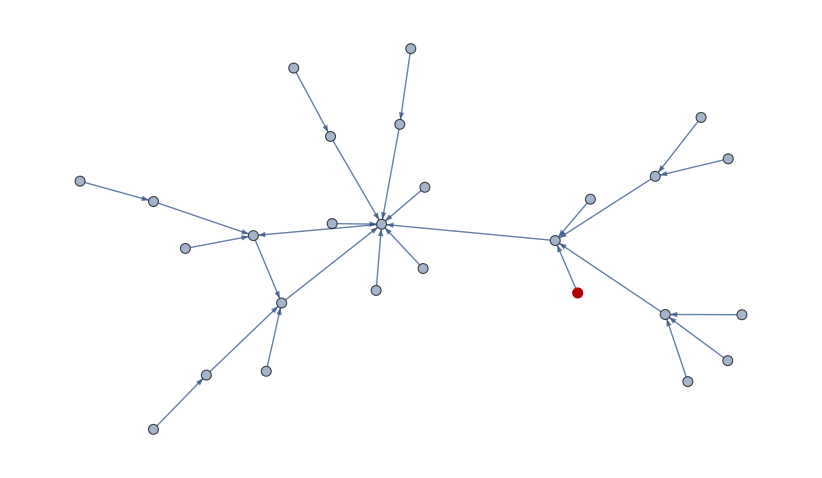

```mathematica
HighlightGraph[seed,27]
```

```mathematica
ConnectedComponents[seed]
```

{{1,2,3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

```mathematica
Position[VertexInDegree[seed],0]
```

{{5},{10},{12},{13},{14},{15},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

```mathematica
Length/@ConnectedComponents[seed]
```

{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Min[Length/@ConnectedComponents[seed]]
```

1

```mathematica
Select[ConnectedComponents[seed],Length[#]==Min[Length/@ConnectedComponents[seed]]&]
```

{{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

```mathematica
Intersection[Position[VertexInDegree[seed],0],Select[ConnectedComponents[seed],Length[#]==Min[Length/@ConnectedComponents[seed]]&]]
```

{{5},{10},{12},{13},{14},{15},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

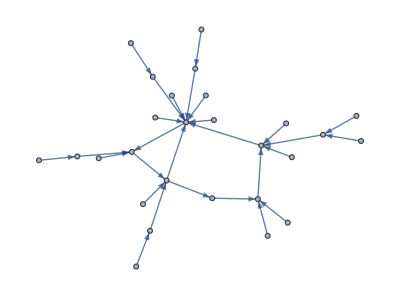

```mathematica
EdgeAdd[seed,RandomChoice[{1,2,3}]->RandomChoice[Flatten[Intersection[Position[VertexInDegree[seed],0],Select[ConnectedComponents[seed],Length[#]==Min[Length/@ConnectedComponents[seed]]&]]]]]
```

```mathematica
ConnectedComponents[%]
```

{{1,2,3,6,9,10},{4},{5},{7},{8},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27}}

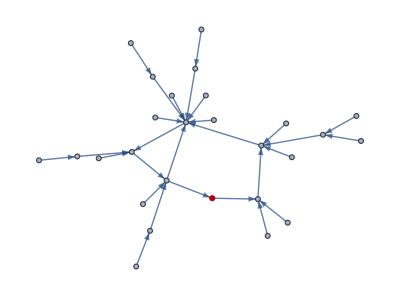

```mathematica
HighlightGraph[%%,10]
```

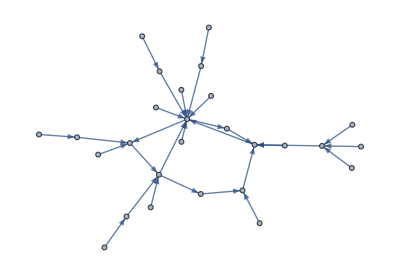

```mathematica
EdgeAdd[%%%,RandomChoice[{1,2,3}]->26]
```

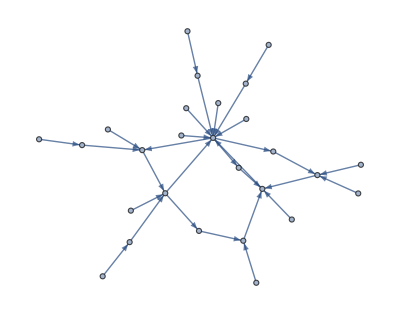

```mathematica
EdgeAdd[%,RandomChoice[{1,2,3}]->25]
```

```mathematica
ConnectedComponents[%]
```

{{1,2,3,6,9,16,25,26,27},{4},{5},{7},{8},{10},{11},{12},{13},{14},{15},{17},{18},{19},{20},{21},{22},{23},{24}}

```mathematica
tst={{0,1,1,1,1},{0,0,1,1,0},{0,1,0,1,1},{1,1,0,0,0},{0,0,0,1,0}};
```

```mathematica
tst=AdjacencyGraph[tst]
```

-Graphics-

```mathematica
Partition[Range[10],2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

```mathematica
graph=graphToNet[tst,Partition[Range[10],2]]
```

{{{1,2},{2,3,4,5}},{{3,4},{3,4,5}},{{5,6},{2,4}},{{7,8},{1,3}},{{9,10},{4}}}

```mathematica
M=Length[graph]
```

5

```mathematica
occ=Transpose[{Range[M],Length/@graph[[All,1]]}]
```

{{1,2},{2,2},{3,2},{4,2},{5,2}}

```mathematica
occ^0/.Indeterminate->0
```

{1,1,0,1,1,1,1,0,1,1}

```mathematica
Off[Power::indet]
```

```mathematica
occ^(1./100)
```

{1.,1.,0.,1.01622,1.00696,1.01396,1.00696,0.,1.,1.}

```mathematica
RandomSample[occ->Range[M],P]
```

```mathematica
Table[RandomSample[occ->Range[10],1],{1000}]//Tally
```

{{{4},295},{{2},47},{{6},240},{{5},126},{{7},123},{{10},59},{{9},65},{{1},45}}

```mathematica
occ=RandomInteger[{0,5},10]
```

{4,2,0,0,4,1,2,4,4,3}

```mathematica
occ^0/.Indeterminate->0
```

Power::indet: Indeterminate expression 0^0 encountered.

{1,1,0,0,1,1,1,1,1,1}

```mathematica
Position[occ,x_/;x>0]
```

{{1},{2},{5},{6},{7},{8},{9},{10}}

```mathematica
Off[Power::indet]
```

```mathematica
occ^(1./100)
```

{1.,1.,0.,1.01622,1.00696,1.01396,1.00696,0.,1.,1.}

```mathematica
occ=Length/@graph[[All,1]]
```

{2,2,2,2,2}

```mathematica
Sort[RandomSample[occ->Range[M],3]]
```

{1,4,5}

```mathematica
Table[RandomSample[occ->Range[10],1],{1000}]//Tally
```

{{{4},295},{{2},47},{{6},240},{{5},126},{{7},123},{{10},59},{{9},65},{{1},45}}

```mathematica
α=0
```

0

```mathematica
remove[g_,P_Integer/;0<P<=M]:=Module[{occ=Length/@g[[All,1]],ret,subset},
If[α==0,Off[Power::indet]];
occ=occ^α;
If[α==0,On[Power::indet];occ=occ/.Indeterminate->0];
Print["occ is ",occ];
subset=Position[occ,x_/;x>0]//Flatten;
Print["subset is ",subset];
subset=If[Length[subset]>P,
Sort[RandomSample[occ->Range[M],P]],
Sort[RandomSample[occ->Range[M],Length[subset]]]
];
Print["subset is ",subset];
Table[If[g[[i,2]]≠{}&&g[[i,1]]!={},{i,RandomChoice[g[[i,2]]]},{i,0}],{i,subset}]
]
```

```mathematica
NestList[updateGraph[#,add[#,remove[#,M]]]&,graph,T]
```

```mathematica
RandomSample[{1,0}->{1,2},2]
```

RandomSample::smplen: RandomSample cannot generate a sample of length 2, which is greater than the length of the sample set {1,0}→{1,2}. If you want a choice of possibly repeated elements from the set, use RandomChoice.

RandomSample[{1,0}→{1,2},2]

```mathematica
remove[twonodes,M]
```

{{1,2}}

```mathematica
graph
```

{{{1,2},{2,3,4,5}},{{3,4},{3,4,5}},{{5,6},{2,4}},{{7,8},{1,3}},{{9,10},{4}}}

```mathematica
α=0
```

0

```mathematica
netEvolve[twonodes,10 NN]
```

RandomSample::smplen: RandomSample cannot generate a sample of length 2, which is greater than the length of the sample set {1,0}→{1,2}. If you want a choice of possibly repeated elements from the set, use RandomChoice.

RandomSample::lrwl: The set of items to sample from, 2, should be a non-empty list or a rule weights -> choices.

Table::iterb: Iterator {i,RandomSample[2,{1,0}→{1,2}]} does not have appropriate bounds.

RandomSample::lrwl: The set of items to sample from, 2, should be a non-empty list or a rule weights -> choices.

General::stop: Further output of RandomSample::lrwl will be suppressed during this calculation.

Table::iterb: Iterator {i,RandomSample[2,{1,0}→{1,2}]} does not have appropriate bounds.

Drop::normal: Nonatomic expression expected at position 1 in Drop[1,1].

Drop::normal: Nonatomic expression expected at position 1 in Drop[2,1].

Drop::normal: Nonatomic expression expected at position 1 in Drop[1,1,{1,2,3,4,5,6,7,8,9,10}].

General::stop: Further output of Drop::normal will be suppressed during this calculation.

Part::partw: Part 2 of {2} does not exist.

Transpose::nmtx: The first two levels of {{Drop[1,1,{1,2,3,4,5,6,7,8,9,10}],Drop[2,1,{}]},{{1,2,3,4,5,6,7,8,9,10},{2}}⟦All,2⟧} cannot be transposed.

RandomSample::wghtv: The weights given on the left-hand side of 1→{1,2} should be a list of positive numerical quantities having the same length as the list given on the right-hand side.

Table::iterb: Iterator {i,RandomSample[2,1→{1,2}]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

RandomSample::wghtv: The weights given on the left-hand side of 1→{1,2} should be a list of positive numerical quantities having the same length as the list given on the right-hand side.

General::stop: Further output of RandomSample::wghtv will be suppressed during this calculation.

$Aborted